# Premier League 21/22 - Data Analysis

## Glossary of the Metrics used in the Code

### xgoals (xG) Definition

The expected goals (xgoals) are the number of goals that can be expected to be scored based on where and how a shot was taken. In this code the xG data were obtained from understat.com

### xgoals Difference (ΔxG) Definition

The xgoals difference (ΔxG) corresponds to the difference between the xG of a team minus the xG of the opponent on a particular match, i.e.  ΔxG=xG-xG_allowed. This is a qualitative metric that in reality represents how much better was the team in question in a particular match.

### Mean xgoals Difference (ΔxG_m) Definition

The mean xgoals difference (ΔxG_m) corresponds to the mean value of the ΔxG metric. This metric corresponds to a specific number that shows how much better was the team in question from its opponent throughout the 21/22 season.

## Directory & Data

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Import the Data

```mathematica
(* Manchester United data *)
datamu=Import[".\\data\\Manchester United Data.txt","Table"];
(* Manchester City data *)
datamc=Import[".\\data\\Manchester City Data.txt","Table"];
(* Liverpool data *)
dataliv=Import[".\\data\\Liverpool Data.txt","Table"];
ndat=Length[datamu]-1
```

38

### Options for Plots

```mathematica
labels={"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38"};
```

## Manchester United - xG Analysis

```mathematica
{Range[datamu[[1]]//Length],datamu[[1]]}//Transpose
```

{{1,Matchweek},{2,Goals_scored},{3,xgoals},{4,Goals_concede},{5,xgoals_allowed},{6,vs}}

```mathematica
(* Table of goals scored by Manchester United in the 21/22 season *)
goalstabmu=Table[{datamu[[i+1,2]],datamu[[i+1,3]]},{i,1,ndat}];
(* Table of xG *)
dxgtabmu=Table[datamu[[i+1,3]]-datamu[[i+1,5]],{i,1,ndat}];
```

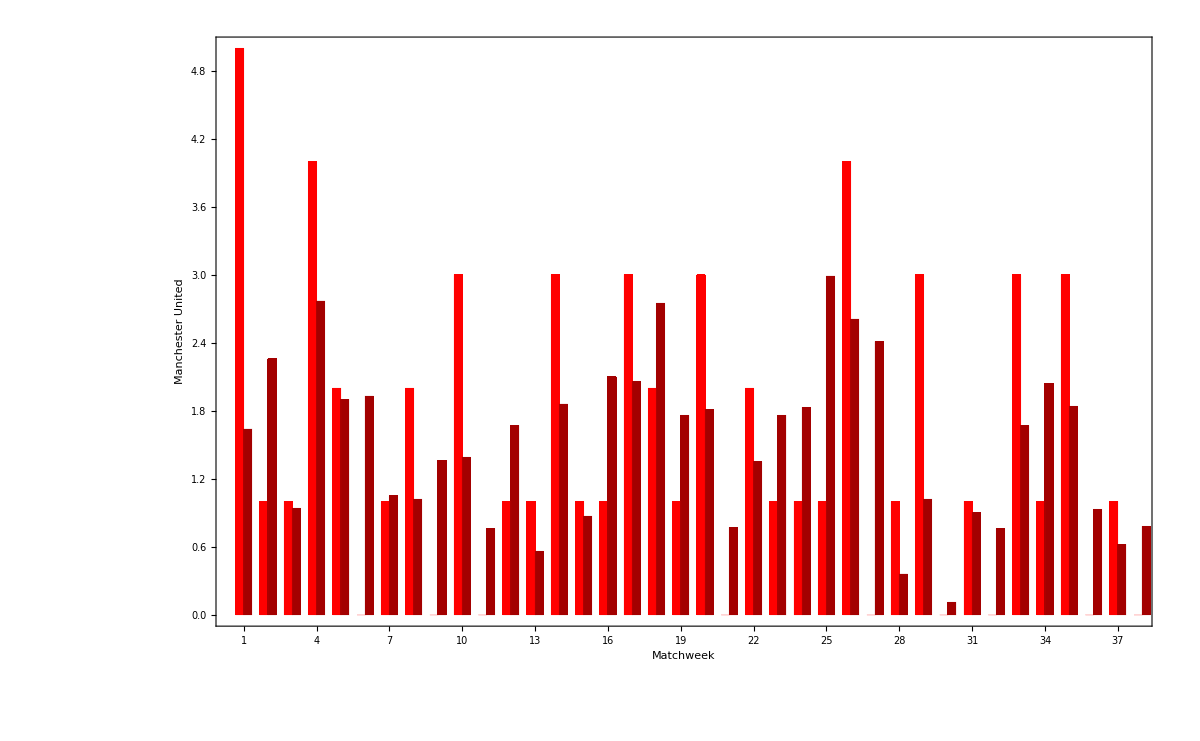

```mathematica
BarChart[goalstabmu,ChartStyle->{Red,RGBColor[0.64,0,0]},ChartLabels->{labels,{None}},Frame->True,FrameLabel->{"Matchweek","Manchester United"},BaseStyle -> {FontFamily -> "Times",17},Epilog->Inset[Framed[Column[{SwatchLegend[{Red,Thick},{"Goals Scored"}],SwatchLegend[{RGBColor[0.64,0,0],Thick},{"xG"}]}],RoundingRadius->5],Scaled[{0.77,0.9}],BaseStyle -> {FontFamily->"Times",11}],LabelStyle->Directive[Black,Large],ImageSize->1200,BarSpacing->{0,1},PlotRange->{{0.8,112},All}]
```

```mathematica
(* Sum of goals scored by Manchester United in the 21/22 season *)
goalsummu=Sum[datamu[[i+1,2]],{i,1,ndat}];
(* Sum of xG *)
xgoalsummu=Sum[datamu[[i+1,3]],{i,1,ndat}];
(* Select the fixtures where ΔxG>0 *)
xgoaldiffposmu=Select[dxgtabmu,#>0&]//Length;
(* Select the fixtures where ΔxG<0 *)
xgoaldifnegmu=Select[dxgtabmu,#<0&]//Length;
Print["Manchester United in the 21/22 season according to the xG analysis should had scored ",xgoalsummu," goals and scored ",goalsummu," goals. Manchester United created better chances in ",Round[100*xgoaldiffposmu/(ndat)//N,0.1],"% of the total matches."]
```

Manchester United in the 21/22 season according to the xG analysis should had scored 57.21 goals and scored 57 goals. Manchester United created better chances in 52.6% of the total matches.

```mathematica
(* Find the number of matches that Manchester United faced top 4 league teams *)
top4mutab=Select[datamu,SameQ[#[[6]],"Liverpool"]||SameQ[#[[6]],"Manchester_City"]||SameQ[#[[6]],"Chelsea"]||SameQ[#[[6]],"Tottenham"]&]
(* Select the matches where ΔxG>0 against a top 4 league team *)
top4posmutab=Select[top4mutab, #[[3]]>#[[5]]&];
(* Select the matches where ΔxG<0 against a top 4 league team *)
top4negmutab=Select[top4mutab, #[[3]]>#[[5]]&];
Print["Manchester United in the 21/22 season according to the xG analysis had ΔxG>0 against a top 4 league team in ",Round[100*Length[top4posmutab]/Length[top4mutab]//N,0.1],"% of the total matches given."]
```

{{9,0,1.36,5,4.05,Liverpool},{10,3,1.39,0,1.16,Tottenham},{11,0,0.76,2,2.04,Manchester_City},{13,1,0.56,1,2.35,Chelsea},{28,1,0.36,4,2.74,Manchester_City},{29,3,1.02,2,1.82,Tottenham},{30,0,0.11,4,2.26,Liverpool},{37,1,0.62,1,2.47,Chelsea}}

Manchester United in the 21/22 season according to the xG analysis had ΔxG>0 against a top 4 league team in 12.5% of the total matches given.

## Manchester City - xG Analysis

```mathematica
(* Table of goals scored by Manchester City in the 21/22 season *)
goalstabmc=Table[{datamc[[i+1,2]],datamc[[i+1,3]]},{i,1,ndat}];
(* Table of xG *)
dxgtabmc=Table[datamc[[i+1,3]]-datamc[[i+1,5]],{i,1,ndat}];
```

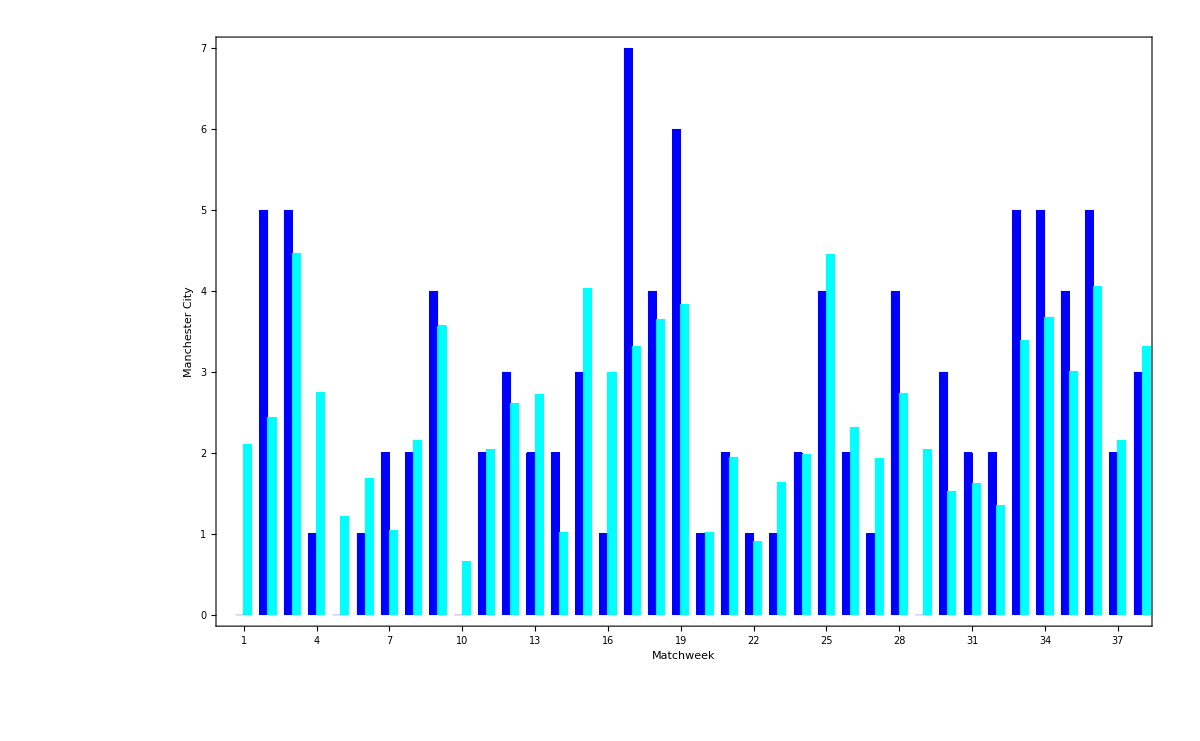

```mathematica
BarChart[goalstabmc,ChartStyle->{Blue,Cyan},ChartLabels->{labels,{None}},Frame->True,FrameLabel->{"Matchweek","Manchester City"},BaseStyle -> {FontFamily -> "Times",17},Epilog->Inset[Framed[Column[{SwatchLegend[{Blue,Thick},{"Goals Scored"}],SwatchLegend[{Cyan,Thick},{"xG"}]}],RoundingRadius->5],Scaled[{0.77,0.9}],BaseStyle -> {FontFamily->"Times",11}],LabelStyle->Directive[Black,Large],ImageSize->1200,BarSpacing->{0,1},PlotRange->{{0.8,112},All}]
```

```mathematica
(* Sum of goals scored by Manchester City in the 21/22 season *)
goalsummc=Sum[datamc[[i+1,2]],{i,1,ndat}];
(* Sum of xG *)
xgoalsummc=Sum[datamc[[i+1,3]],{i,1,ndat}];
(* Select the fixtures where ΔxG>0 *)
xgoalposmc=Select[dxgtabmc,#>0&]//Length;
(* Select the fixtures where ΔxG<0 *)
xgoalnegmc=Select[dxgtabmc,#<0&]//Length;
Print["Manchester City in the 21/22 season according to the xG analysis should had scored ",xgoalsummc," goals and scored ",goalsummc," goals. Manchester City created better chances in ",Round[100*xgoalposmc/(ndat)//N,0.1],"% of the total matches given."]
```

Manchester City in the 21/22 season according to the xG analysis should had scored 93.39 goals and scored 99 goals. Manchester City created better chances in 97.4% of the total matches given.

```mathematica
(* Find the number of matches that Manchester City faced top 4 league teams *)
top4mctab=Select[datamc,SameQ[#[[6]],"Liverpool"]||SameQ[#[[6]],"Manchester_United"]||SameQ[#[[6]],"Chelsea"]||SameQ[#[[6]],"Tottenham"]&]
(* Select the matches where ΔxG>0 against a top 4 league team *)
top4posmctab=Select[top4mctab, #[[3]]>#[[5]]&];
(* Select the matches where ΔxG<0 against a top 4 league team *)
top4negmctab=Select[top4mctab, #[[3]]>#[[5]]&];
Print["Manchester City in the 21/22 season according to the xG analysis had ΔxG>0 against a top 4 league team in ",Round[100*Length[top4posmctab]/Length[top4mctab]//N,0.1],"% of the matches given."]
```

{{1,0,2.11,1,1.06,Tottenham},{6,1,1.69,0,0.19,Chelsea},{7,2,1.04,2,0.95,Liverpool},{11,2,2.04,0,0.76,Manchester_United},{22,1,0.9,0,0.61,Chelsea},{26,2,2.32,3,2.,Tottenham},{28,4,2.74,1,0.36,Manchester_United},{32,2,1.35,2,1.3,Liverpool}}

Manchester City in the 21/22 season according to the xG analysis had ΔxG>0 against a top 4 league team in 100.% of the matches given.

## Liverpool - xG Analysis

```mathematica
(* Table of goals scored by Liverpool in the 21/22 season *)
goalstabliv=Table[{dataliv[[i+1,2]],dataliv[[i+1,3]]},{i,1,ndat}];
(* Table of xG *)
dxgtabliv=Table[dataliv[[i+1,3]]-dataliv[[i+1,5]],{i,1,ndat}];
```

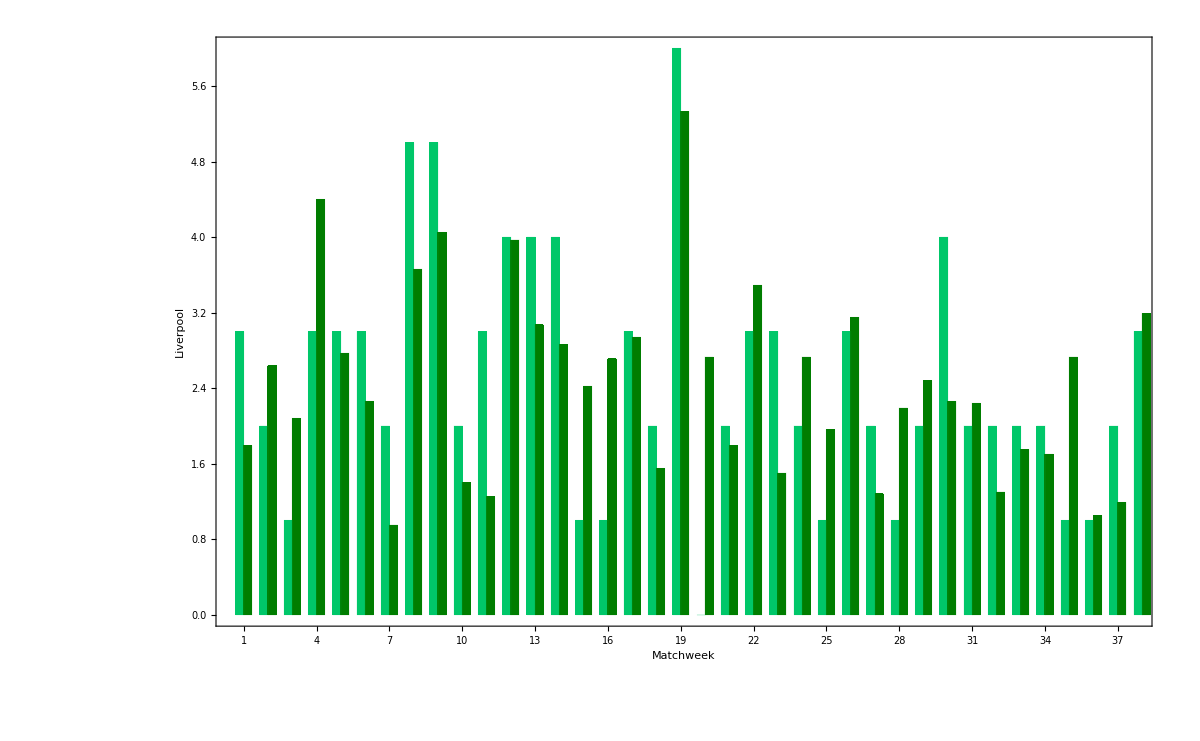

```mathematica
BarChart[goalstabliv,ChartStyle->{RGBColor[0,0.78,0.41],RGBColor[0,0.49,0]},ChartLabels->{labels,{None}},Frame->True,FrameLabel->{"Matchweek","Liverpool"},BaseStyle -> {FontFamily -> "Times",17},Epilog->Inset[Framed[Column[{SwatchLegend[{RGBColor[0,0.78,0.41],Thick},{"Goals Scored"}],SwatchLegend[{RGBColor[0,0.49,0],Thick},{"xG"}]}],RoundingRadius->5],Scaled[{0.77,0.9}],BaseStyle -> {FontFamily->"Times",11}],LabelStyle->Directive[Black,Large],ImageSize->1200,BarSpacing->{0,1},PlotRange->{{0.8,112},All}]
```

```mathematica
(* Sum of goals scored by Liverpool in the 21/22 season *)
goalsumliv=Sum[dataliv[[i+1,2]],{i,1,ndat}];
(* Sum of xG *)
xgoalsumliv=Sum[dataliv[[i+1,3]],{i,1,ndat}];
(* Select the fixtures where ΔxG>0 *)
xgoalposliv=Select[dxgtabliv,#>0&]//Length;
(* Select the fixtures where ΔxG<0 *)
xgoalnegliv=Select[dxgtabliv,#<0&]//Length;
```

```mathematica
Print["Liverpool in the 21/22 season according to the xG analysis should had scored ",xgoalsumliv," goals and scored ",goalsumliv," goals. Liverpool created better chances in ",Round[100*xgoalposliv/(ndat)//N,0.1],"% of the total matches given."]
```

Liverpool in the 21/22 season according to the xG analysis should had scored 92.81 goals and scored 95 goals. Liverpool created better chances in 81.6% of the total matches given.

```mathematica
(* Find the number of matches that Liverpool faced top 4 league teams *)
top4livtab=Select[dataliv,SameQ[#[[6]],"Manchester_City"]||SameQ[#[[6]],"Manchester_United"]||SameQ[#[[6]],"Chelsea"]||SameQ[#[[6]],"Tottenham"]&]
(* Select the matches where ΔxG>0 against a top 4 league team *)
top4poslivtab=Select[top4livtab, #[[3]]>#[[5]]&];
(* Select the matches where ΔxG<0 against a top 4 league team *)
top4neglivtab=Select[top4livtab, #[[3]]>#[[5]]&];
Print["Liverpool in the 21/22 season according to the xG analysis had ΔxG>0 against a top 4 league team in ",Round[100*Length[top4poslivtab]/Length[top4livtab]//N,0.1],"% of the matches given."]
```

{{3,1,2.08,1,0.57,Chelsea},{7,2,0.95,2,1.04,Manchester_City},{9,5,4.05,0,1.36,Manchester_United},{18,2,1.55,2,2.8,Tottenham},{21,2,1.79,2,1.39,Chelsea},{30,4,2.26,0,0.11,Manchester_United},{32,2,1.3,2,1.35,Manchester_City},{36,1,1.05,1,0.98,Tottenham}}

Liverpool in the 21/22 season according to the xG analysis had ΔxG>0 against a top 4 league team in 62.5% of the matches given.

## Combined Plots- xG Analysis

### Pie Chart Plot

```mathematica
mutop4pos=Round[100*Length[top4posmutab]/Length[top4mutab]//N,0.1];
chartmu=PieChart[{mutop4pos,100-mutop4pos},ChartStyle->{RGBColor[1.,0.6,0.57],RGBColor[1.,0.25,0.18]},ChartLabels->{"12.5%","87.5%"},PlotLabel->"Manchester United"];
mctop4pos=Round[100*Length[top4posmctab]/Length[top4mctab]//N,0.1];
chartmc=PieChart[{mctop4pos,100-mctop4pos},ChartStyle->{Cyan,Blue},ChartLabels->{"100%","0%"},PlotLabel->"Manchester City"];
livtop4pos=Round[100*Length[top4poslivtab]/Length[top4livtab]//N,0.1];
chartliv=PieChart[{livtop4pos,100-livtop4pos},ChartStyle->{RGBColor[0.5,0.93,0.24],RGBColor[0.24,0.8,0.56]},ChartLabels->{"62.5%","37.5%"},PlotLabel->"Liverpool"];
```

```mathematica
Legended[Grid[{{chartmu,chartmc,chartliv}}],Placed[SwatchLegend[{RGBColor[1.,0.6,0.57],RGBColor[1.,0.25,0.18],Cyan,Blue,RGBColor[0.5,0.93,0.24],RGBColor[0.24,0.8,0.56]},{"Manchester United's ΔxG>0 from its opponent (against top 4 clubs)","Manchester United's ΔxG<0 from its opponent (against top 4 clubs)","Manchester City's ΔxG>0 from its opponent (against top 4 clubs)","Manchester City's ΔxG<0 from its opponent (against top 4 clubs)","Liverpool's ΔxG>0 from its opponent (against top 4 clubs)","Liverpool's ΔxG<0 from its opponent (against top 4 clubs)"},LegendLayout->{"Column",2}],Below]]
```

-Graphics-

### ΔxG Plot

```mathematica
dxgmuplt=ListLinePlot[dxgtabmu,Frame->True,BaseStyle -> {FontFamily -> "Times",23},LabelStyle->Directive[Black,Large],ImageSize->1200,PlotRange->All,PlotStyle->Red];
dxgmcplt=ListLinePlot[dxgtabmc,Frame->True,BaseStyle -> {FontFamily -> "Times",23},LabelStyle->Directive[Black,Large],ImageSize->1200,PlotRange->All,PlotStyle->Blue];
dxglivplt=ListLinePlot[dxgtabliv,Frame->True,BaseStyle -> {FontFamily -> "Times",23},LabelStyle->Directive[Black,Large],ImageSize->1200,PlotRange->All,PlotStyle->RGBColor[0,0.78,0.41]];
```

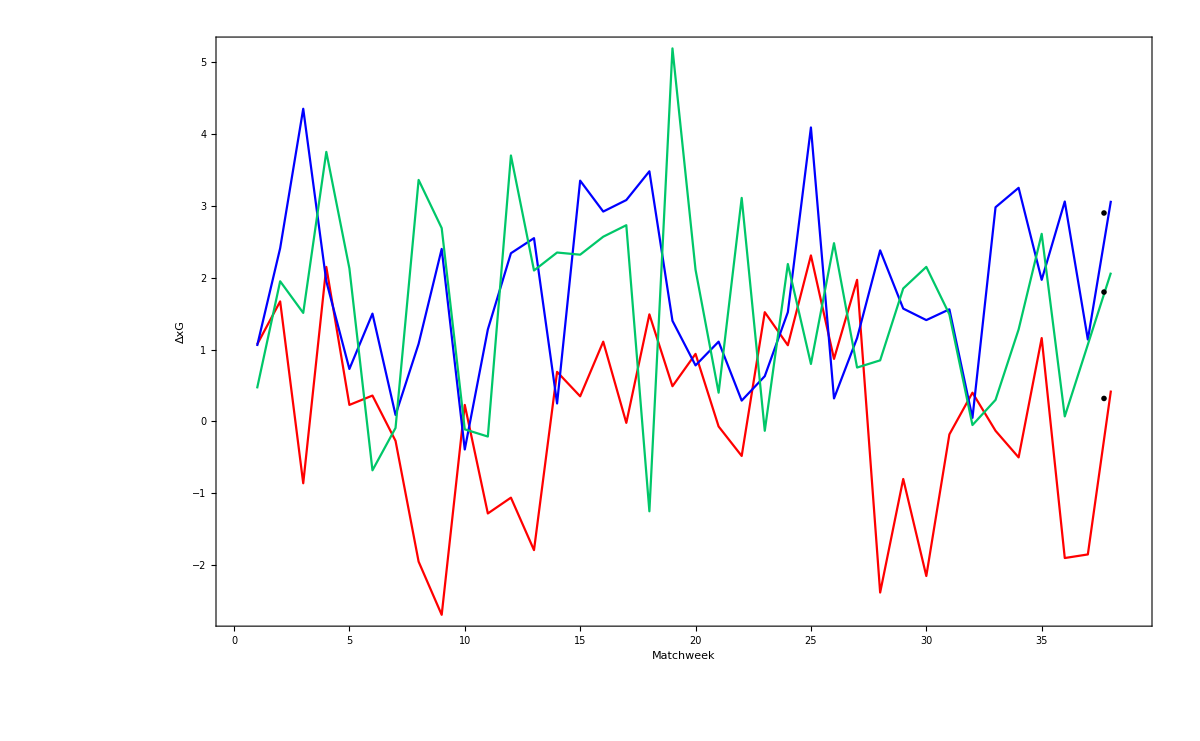

```mathematica
imgmu=Import["manchester_united.png"];
imgmc=Import["manchester_city.png"];
imgliv=Import["liverpool.png"];
Show[dxgmuplt,dxgmcplt,dxglivplt,PlotRange->{{0,39},All},FrameLabel->{"Matchweek","ΔxG"},Epilog->{Inset[imgmu,{37.7,0.32},{0,0},Scaled[0.08]],Inset[imgliv,{37.7,1.8},{0,0},Scaled[0.11]],Inset[imgmc,{37.7,2.9},{0,0},Scaled[0.08]]}]
```

### ΔxG_m Plot

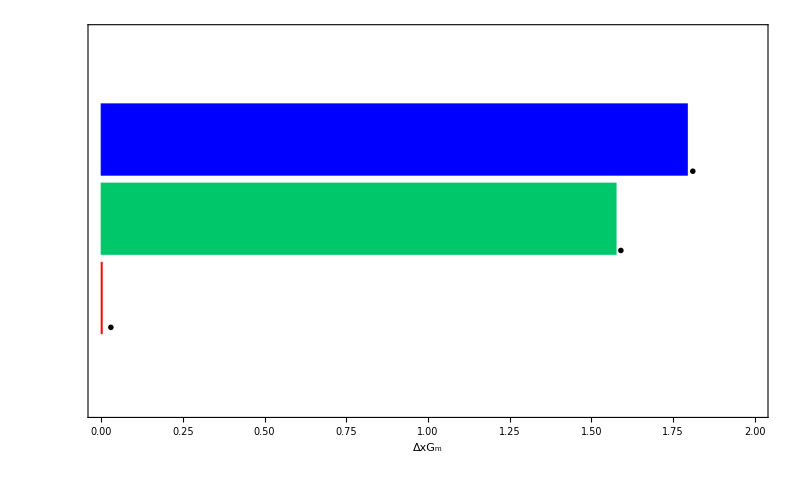

```mathematica
meanmu=Mean[dxgtabmu];
meanmc=Mean[dxgtabmc];
meanliv=Mean[dxgtabliv];
BarChart[{meanmu,meanliv,meanmc},BarOrigin->Left,ChartStyle->{Red,RGBColor[0,0.78,0.41],Blue},Frame->True,BaseStyle -> {FontFamily -> "Times",17},ImageSize->800,Epilog->{Inset[imgmu,{0.03,0.63},{0,0},Scaled[0.17]],Inset[imgliv,{1.59,1.6},{0,0},Scaled[0.17]],Inset[imgmc,{1.81,2.6},{0,0},Scaled[0.17]]},PlotRange->{0,2},FrameLabel->{"","ΔxG_m"},LabelStyle->Directive[Black,Large]]
```